```mathematica
(*2015*)
sensUp0={14,45.7,11.3,12.4,13.7,9.83,9.6,24.5,12.6};
sensUpSmallPos={9.1,8.8,22.3,35.8,11.3,22.7,11.5};
sensUpSmallNeg={23.8,26.3,13,19,46.5,11,20.5};
sensUpBigPos={21.4,14.4,7.9,8.2,12.4,7.4,11.9};
sensUpBigNeg={26,57,20.9,19.2,12.5,18.4,11.9,11.8,17.9};
sensDown0={31,24,16.4,16.5,8.7,8.9};
sensDownSmallPos={23.6,18.7,23.7,20.8,12.2,14.4,19.3,31.7,20.7,15.1,19.5};
sensDownSmallNeg={30.6,19,15.2,32.5,14.6,11.2,20.6,9.22,9.8,20};
sensDownBigPos={29,29,12.1,14.4,13.8,10.1};
sensDownBigNeg={17,10,21.1,10.6,12.8,28.1};
sens=Table[0,{k,1,10}];
Dimensions[sensUp0]+Dimensions[sensUpSmallPos]+Dimensions[sensUpSmallNeg]+Dimensions[sensUpBigPos]+Dimensions[sensUpBigNeg]+Dimensions[sensDown0]+Dimensions[sensDownSmallPos]+Dimensions[sensDownSmallNeg]+Dimensions[sensDownBigPos]+Dimensions[sensDownBigNeg]
sens[[1]]=√(1/Total[1/sensUp0^2]);
sens[[2]]=√(1/Total[1/sensUpSmallPos^2]);
sens[[3]]=√(1/Total[1/sensUpSmallNeg^2]);
sens[[4]]=√(1/Total[1/sensUpBigPos^2]);
sens[[5]]=√(1/Total[1/sensUpBigNeg^2]);
sens[[6]]=√(1/Total[1/sensDown0^2]);
sens[[7]]=√(1/Total[1/sensDownSmallPos^2]);
sens[[8]]=√(1/Total[1/sensDownSmallNeg^2]);
sens[[9]]=√(1/Total[1/sensDownBigPos^2]);
sens[[10]]=√(1/Total[1/sensDownBigNeg^2]);

sens
√(1/Total[1/sens^2])
sensall=Join[sensUp0,sensUpSmallPos,sensUpSmallNeg,sensUpBigPos,sensUpBigNeg,sensDown0,sensDownSmallPos,sensDownSmallNeg,sensDownBigPos,sensDownBigNeg];
senscum=Table[0,{k,1,Dimensions[sensall][[1]]}];
For[i=1,i<=Dimensions[sensall][[1]],i++,
senscum[[i]]=√(1/(∑_(j=1)^i (1/sensall[[j]]^2)));
];
senscum
```

{78}

{4.28714,4.7081,6.59311,3.78701,5.46299,5.27015,5.47855,4.52639,5.86364,5.59224}

1.57144

{14,13.386,8.63471,7.08597,6.29393,5.30053,4.64021,4.55916,4.28714,3.8783,3.54893,3.50482,3.48815,3.33296,3.29761,3.16986,3.14212,3.11993,3.03378,2.99583,2.98963,2.88498,2.85683,2.83171,2.7785,2.62111,2.49666,2.44754,2.32374,2.28066,2.27194,2.27014,2.25686,2.24143,2.20624,2.19055,2.15436,2.11932,2.10462,2.09979,2.0918,2.07499,2.05877,2.00344,1.95453,1.94786,1.93738,1.93094,1.92267,1.89923,1.88293,1.87403,1.87076,1.86317,1.84915,1.84089,1.83757,1.82903,1.81593,1.8131,1.79928,1.7765,1.76994,1.7382,1.71149,1.70525,1.70231,1.69939,1.68287,1.6715,1.65937,1.63742,1.62987,1.60865,1.60399,1.58594,1.5739,1.57144}

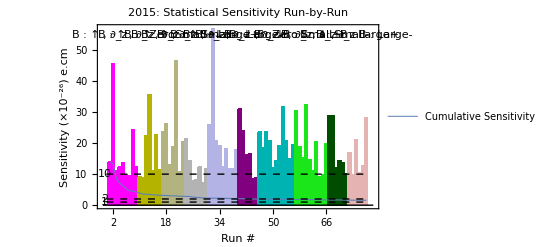

```mathematica
lineStyle={Thick,Black,Dashed};
line1=Line[{{0,2},{78,2}}];
line2=Line[{{0,1},{78,1}}];
line3=Line[{{0,10},{78,10}}];
Show[BarChart[{sensUp0,sensUpSmallPos,sensUpSmallNeg,sensUpBigPos,sensUpBigNeg,sensDown0,sensDownSmallPos,sensDownSmallNeg,sensDownBigPos,sensDownBigNeg},BarSpacing->0,BaseStyle->AbsoluteThickness[3],LabelStyle->{18},ChartStyle->{{RGBColor[1,0,1],RGBColor[.7,.7,0],RGBColor[.7,.7,.5],RGBColor[.7,.7,.7],RGBColor[.7,.7,.9],RGBColor[.5,0,.5],RGBColor[0,.7,.7],RGBColor[.1,.9,.1],RGBColor[0,.3,0],RGBColor[.9,.7,.7],RGBColor[1,0,0]},None}],ListLinePlot[senscum,PlotRange->All,PlotStyle->Thickness[0.002],PlotLegends->{"Cumulative Sensitivity"},LabelStyle->{18}],Epilog->{{Directive[lineStyle],line1,line2,line3},Text[Style["1",FontSize->Medium],{-.5,1}],Text[Style["2",FontSize->Medium],{-.5,2}],Rotate[Text[Style["10",FontSize->Medium],{-.5,10}],0],
Rotate[Text[Style["B : ↑ , ∂_z B : Zero",FontSize->Medium],{5,55}],45Degree],
Rotate[Text[Style["B : ↑ , ∂_z B : Small+",FontSize->Medium],{15,55}],45Degree],
Rotate[Text[Style["B : ↑ , ∂_z B : Small-",FontSize->Medium],{22,55}],45Degree],
Rotate[Text[Style["B : ↑ , ∂_z B : Large+",FontSize->Medium],{28,55}],45Degree],
Rotate[Text[Style["B : ↑ , ∂_z B : Large-",FontSize->Medium],{36,55}],45Degree],
Rotate[Text[Style["B : ↓ , ∂_z B : Zero",FontSize->Medium],{42,55}],45Degree],
Rotate[Text[Style["B : ↓ , ∂_z B : Small+",FontSize->Medium],{53,55}],45Degree],
Rotate[Text[Style["B : ↓ , ∂_z B : Small-",FontSize->Medium],{62,55}],45Degree],
Rotate[Text[Style["B : ↓ , ∂_z B : Large+",FontSize->Medium],{70,55}],45Degree],
Rotate[Text[Style["B : ↓ , ∂_z B : Large-",FontSize->Medium],{75,55}],45Degree]},
Frame->True,LabelStyle->{18},ImageSize->{1250},FrameLabel->{"Run #","Sensitivity (×10^-26) e.cm"},FrameTicks->{{Automatic,None},{Table[2k,{k,1,39}],None}},PlotLabel->"2015: Statistical Sensitivity Run-by-Run"]
```

```mathematica
(*2016:<=11218*)
```

```mathematica
sensUp02={10.9,16.3};
sensUpSmallPos2={8.5};
sensUpSmallNeg2={9.98};
sensUpBigPos2={9.4};
sensUpBigNeg2={7.97};
sensDown02={7.59};
sensDownSmallPos2={10.2};
sensDownSmallNeg2={};
sensDownBigPos2={9.54,10.9,20.1,36.5};
sensDownBigNeg2={};
sens2=Table[0,{k,1,10}];
Dimensions[sensUp02]+Dimensions[sensUpSmallPos2]+Dimensions[sensUpSmallNeg2]+Dimensions[sensUpBigPos2]+Dimensions[sensUpBigNeg2]+Dimensions[sensDown02]+Dimensions[sensDownSmallPos2]+Dimensions[sensDownSmallNeg2]+Dimensions[sensDownBigPos2]+Dimensions[sensDownBigNeg2]
sens2[[1]]=√(1/Total[1/sensUp02^2]);
sens2[[2]]=√(1/Total[1/sensUpSmallPos2^2]);
sens2[[3]]=√(1/Total[1/sensUpSmallNeg2^2]);
sens2[[4]]=√(1/Total[1/sensUpBigPos2^2]);
sens2[[5]]=√(1/Total[1/sensUpBigNeg2^2]);
sens2[[6]]=√(1/Total[1/sensDown02^2]);
sens2[[7]]=√(1/Total[1/sensDownSmallPos2^2]);
sens2[[8]]=√(1/Total[1/sensDownSmallNeg2^2]);
sens2[[9]]=√(1/Total[1/sensDownBigPos2^2]);
sens2[[10]]=√(1/Total[1/sensDownBigNeg2^2]);

sens2
√(1/Total[1/sens2^2])
sensall2=Join[sensUp02,sensUpSmallPos2,sensUpSmallNeg2,sensUpBigPos2,sensUpBigNeg2,sensDown02,sensDownSmallPos2,sensDownSmallNeg2,sensDownBigPos2,sensDownBigNeg2];
senscum2=Table[0,{k,1,Dimensions[sensall2][[1]]}];
For[i=1,i<=Dimensions[sensall2][[1]],i++,
senscum2[[i]]=√(1/(∑_(j=1)^i (1/sensall2[[j]]^2)));
];
senscum2
```

{12}

Power::infy: Infinite expression 1/0 encountered.

{9.06079,8.5,9.98,9.4,7.97,7.59,10.2,ComplexInfinity,6.64746,ComplexInfinity}

2.97848

{10.9,9.06079,6.19918,5.26596,4.59418,3.98025,3.52497,3.33163,3.14534,3.02204,2.98845,2.97848}

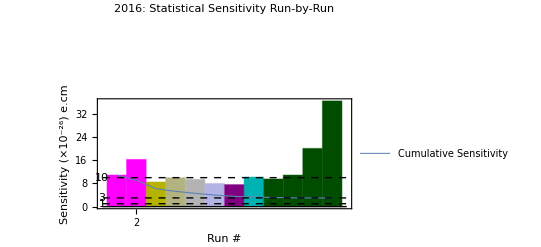

```mathematica
lineStyle={Thick,Black,Dashed};
line1=Line[{{.3,3},{78,3}}];
line2=Line[{{.3,1},{78,1}}];
line3=Line[{{.3,10},{78,10}}];
Show[BarChart[{sensUp02,sensUpSmallPos2,sensUpSmallNeg2,sensUpBigPos2,sensUpBigNeg2,sensDown02,sensDownSmallPos2,sensDownSmallNeg2,sensDownBigPos2,sensDownBigNeg2},BarSpacing->0,BaseStyle->AbsoluteThickness[3],LabelStyle->{18},ChartStyle->{{RGBColor[1,0,1],RGBColor[.7,.7,0],RGBColor[.7,.7,.5],RGBColor[.7,.7,.7],RGBColor[.7,.7,.9],RGBColor[.5,0,.5],RGBColor[0,.7,.7],RGBColor[.1,.9,.1],RGBColor[0,.3,0],RGBColor[.9,.7,.7],RGBColor[1,0,0]},None}],ListLinePlot[senscum2,PlotRange->All,PlotStyle->Thickness[0.002],PlotLegends->{"Cumulative Sensitivity"},LabelStyle->{18}],Epilog->{{Directive[lineStyle],line1,line2,line3},Text[Style["1",FontSize->Medium],{.25,1}],Text[Style["3",FontSize->Medium],{0.25,3}],Rotate[Text[Style["10",FontSize->Medium],{0.25,10}],0],
Rotate[Text[Style["B : ↑ , ∂_z B : Zero",FontSize->Medium],{5,55}],45Degree],
Rotate[Text[Style["B : ↑ , ∂_z B : Small+",FontSize->Medium],{15,55}],45Degree],
Rotate[Text[Style["B : ↑ , ∂_z B : Small-",FontSize->Medium],{22,55}],45Degree],
Rotate[Text[Style["B : ↑ , ∂_z B : Large+",FontSize->Medium],{28,55}],45Degree],
Rotate[Text[Style["B : ↑ , ∂_z B : Large-",FontSize->Medium],{36,55}],45Degree],
Rotate[Text[Style["B : ↓ , ∂_z B : Zero",FontSize->Medium],{42,55}],45Degree],
Rotate[Text[Style["B : ↓ , ∂_z B : Small+",FontSize->Medium],{53,55}],45Degree],
Rotate[Text[Style["B : ↓ , ∂_z B : Small-",FontSize->Medium],{62,55}],45Degree],
Rotate[Text[Style["B : ↓ , ∂_z B : Large+",FontSize->Medium],{70,55}],45Degree],
Rotate[Text[Style["B : ↓ , ∂_z B : Large-",FontSize->Medium],{75,55}],45Degree]},
Frame->True,LabelStyle->{18},ImageSize->{1250},FrameLabel->{"Run #","Sensitivity (×10^-26) e.cm"},FrameTicks->{{Automatic,None},{Table[2k,{k,1,39}],None}},PlotLabel->"2016: Statistical Sensitivity Run-by-Run"]
```